```mathematica
131071(1/(125000000))//N
```

0.00104857

```mathematica
65536(1/(125000000))//N
```

0.000524288

```mathematica
(0.001048568+0.000524288)1000
```

1.57286

```mathematica
8192+4096
```

12288

```mathematica
Mod[8192+4096+4000,8192 2]
```

104

```mathematica
Clear["Global`*"]
```

```mathematica
8192+4096+1200
```

13488

```mathematica
f[τ_]=1/(√(1-(Tanh[(q E τ)/(m c)])^2));
x[τ_] = (m c^2)/(q E)(Cosh[(q E τ)/(m c)]-1);
```

```mathematica
FullSimplify[D[f[τ],τ]/(D[x[τ],τ])]
```

(ⅇ q Cosh[(ⅇ q τ)/(c m)] √(Sech[(ⅇ q τ)/(c m)]^2))/(c^2 m)

```mathematica
x1[τ_] = -v(m c)/(q B)( Cos[(q B)/(m c) τ]-1);
```

```mathematica
x2[τ_] = v(m c)/(q B)Sin[(q B)/(m c) τ];
```

```mathematica
D[x2[τ],τ]
```

v Cos[(B q τ)/(c m)]

```mathematica
Cross[{a,b,0},{0 ,0,c}]
```

{b c,-a c,0}

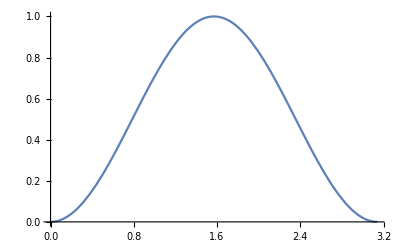

```mathematica
Plot[Sin[x]^2,{x,0,Pi}]
```

```mathematica
f[θ_] = Sin[θ]^2/(1-β Cos[θ])^5
```

Sin[θ]^2/(1-β Cos[θ])^5

```mathematica
fp[θ_]=D[f[θ],θ]
```

(2 Cos[θ] Sin[θ])/(1-β Cos[θ])^5-(5 β Sin[θ]^3)/(1-β Cos[θ])^6

```mathematica
fp'[0]
```

2/(1-β)^5

```mathematica
PolarPlot[Sin[θ]^2/(1-Cos[θ])^6,{θ,0, π}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

-Graphics-

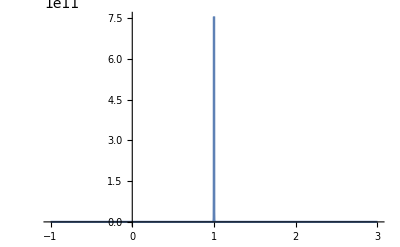

```mathematica
Plot[(1-x^2)/(1-x)^5,{x,-1,3},PlotRange->All]
```

```mathematica
1/(4^5)
```

1/1024

```mathematica
Numerator[1/1024]
```

1

```mathematica
Sum[n^2 (1/2^t)Binomial[t,(n+t)/2],{n,-Infinity,Infinity}]
```

1/(4+t)2^-t (8 Binomial[t,1/2 (-2+t)]+6 t Binomial[t,1/2 (-2+t)]+t^2 Binomial[t,1/2 (-2+t)]-16 Binomial[t,1/2 (-2+t)] Hypergeometric2F1[3,2-t/2,3+t/2,-1]+8 t Binomial[t,1/2 (-2+t)] Hypergeometric2F1[3,2-t/2,3+t/2,-1]+4 Binomial[t,1/2 (-1+t)] HypergeometricPFQ[{1,3/2,3/2,1/2-t/2},{1/2,1/2,3/2+t/2},-1]+t Binomial[t,1/2 (-1+t)] HypergeometricPFQ[{1,3/2,3/2,1/2-t/2},{1/2,1/2,3/2+t/2},-1])+1/(4+t)2^-t (8 Binomial[t,(2+t)/2]+6 t Binomial[t,(2+t)/2]+t^2 Binomial[t,(2+t)/2]-16 Binomial[t,(2+t)/2] Hypergeometric2F1[3,2-t/2,3+t/2,-1]+8 t Binomial[t,(2+t)/2] Hypergeometric2F1[3,2-t/2,3+t/2,-1]+4 Binomial[t,(1+t)/2] HypergeometricPFQ[{1,3/2,3/2,1/2-t/2},{1/2,1/2,3/2+t/2},-1]+t Binomial[t,(1+t)/2] HypergeometricPFQ[{1,3/2,3/2,1/2-t/2},{1/2,1/2,3/2+t/2},-1])

```mathematica
Integrate[n^2 Exp[-n^2 / (2t)],{n,-Infinity,Infinity}]/Sqrt[2 Pi t]
```

ConditionalExpression[1. t,Re[t]>0]